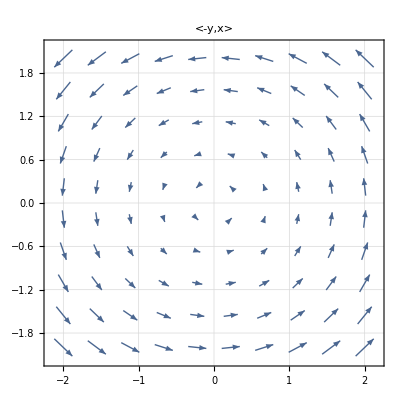

```mathematica
Show[{
VectorPlot[{-y,x},{x,-2,2},{y,-2,2},GridLines->Automatic,VectorPoints->10,VectorScale->Small,PlotLabel->Style["<-y,x>",24]](*,
Graphics @ Table[Circle[{0,0},k],{k,1/2,2,1/2}] *)
}]
```

```mathematica
VectorPlot3D[{0,0,z},{x,-1,1},{y,-1,1},{z,-1,1},VectorPoints->5,VectorScale->Small,PlotLabel->Style["<0,0,z>",24]]
```

-Graphics3D-

```mathematica
VectorPlot3D[{y,z,x},{x,-1,1},{y,-1,1},{z,-1,1},VectorPoints->5,PlotLabel->Style["<y,z,x>",24],VectorScale->Small]
```

-Graphics3D-

```mathematica
VectorPlot3D[{y,-2,x},{x,-1,1},{y,-1,1},{z,-1,1},VectorPoints->5,PlotLabel->Style["<y,-2,x>",24],VectorScale->Small]
```

-Graphics3D-

```mathematica
VectorPlot3D[{y/z,-x/z,z/4},{x,-1,1},{y,-1,1},{z,-1,1},VectorPoints->5,PlotLabel->Style["<y/z, -x/z, z/4>",24],VectorScale->Small]
```

-Graphics3D-

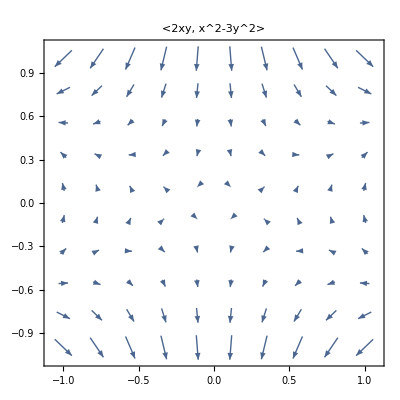

```mathematica
vp=VectorPlot[Grad[x^2y-y^3,{x,y}],{x,-1,1},{y,-1,1},VectorPoints->10,PlotLabel->Style["<2xy, x^2-3y^2>",24],VectorScale->Small]
```

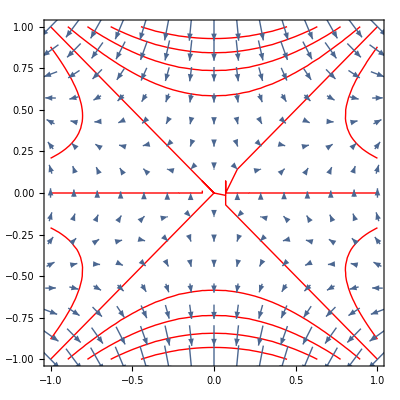

```mathematica
Show[{
ContourPlot[x^2y-y^3,{x,-1,1},{y,-1,1},ContourShading->None,PerformanceGoal->"Quality",ContourStyle->Red],
VectorPlot[Grad[x^2y-y^3,{x,y}],{x,-1,1},{y,-1,1},VectorPoints->15,PlotLabel->Style["<2xy, x^2-3y^2>",24],VectorScale->Small]
}]
```

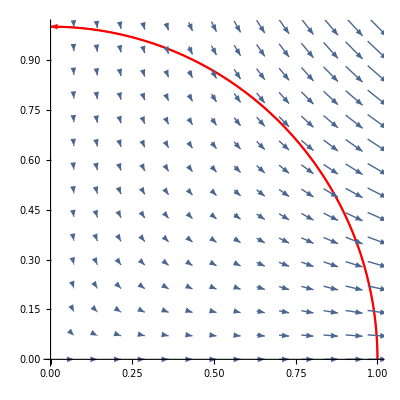

```mathematica
pts=N@Table[{Cos[k],Sin[k]},{k,0,Pi/2,Pi/200}];
Show[{
 ParametricPlot[{Cos[t],Sin[t]},{t,0,Pi/2},PlotStyle->Red],
Graphics[{Red,Arrow[pts,0]}],
VectorPlot[{x^2,-x y},{x,0,1},{y,0,1},GridLines->Automatic,VectorPoints->15,VectorScale->Small]
}]
```

```mathematica
?Arrow
```

Arrow[{pt_1,pt_2}] is a graphics primitive that represents an arrow from pt_1 to pt_2.
Arrow[{pt_1,pt_2},s] represents an arrow with its ends set back from pt_1 and pt_2 by a distance s. 
Arrow[{pt_1,pt_2},{s_1,s_2}] sets back by s_1 from pt_1 and s_2 from pt_2. 
Arrow[curve,…] represents an arrow following the specified curve.



```mathematica
Graphics[Circle[{0,0},3]]
```

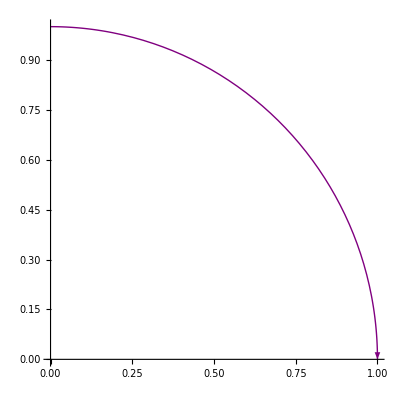

```mathematica
r1=ParametricPlot[{Sin[t],Cos[t]},{t,0,Pi/2},PlotStyle->{Thick,Purple}]/.Line->Arrow
```

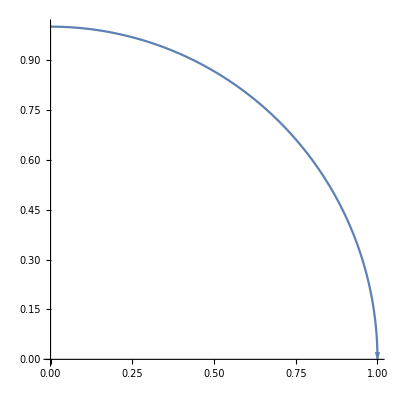

```mathematica
PlotStyle->{Thick,Purple}]/.Line->Arrow
```

```mathematica
Animate[ParametricPlot[{Cos[t],Sin[t]},{t,a,a+2 Pi-Pi/8},Axes->False,PlotStyle->{Thick,Purple}]/.Line->Arrow,{a,0,10}]
```

```mathematica
Manipulate[pts=N@Table[{Cos[k],Sin[k]}*r+o,{k,α Degree,β Degree,(β Degree-α Degree)/d}];
Show[Graphics[{Lighter@Pink,AbsoluteThickness@10,Circle[o,r,{α Degree,β Degree}]}],Graphics[{Arrow[pts,0]}],PlotRange->{{-1.3,1.3},{-1.3,1.3}},AspectRatio->1,Axes->True,ImageSize->250],{{d,20,"res."},1,100,Appearance->"Labeled"},{{α,0,"α"},0,360,Appearance->"Labeled"},{{β,250,"β"},0,360,Appearance->"Labeled"},{{r,1,"r"},0.01,2,Appearance->"Labeled"},{{o,{0,0},"origo"},{-1,-1},{1,1}},ControlPlacement->Left]
```